## plotting tool for paper-quality figures

```mathematica
(*
AppendTo[$Path, "/Users/fernando/Dropbox/Research/Mathematica Notebooks/MyPackages"]*)
```

{/Applications/Mathematica.app/Contents/AddOns/Applications,/Users/fernando/Library/Mathematica/DocumentationIndices,/Applications/Mathematica.app/Contents/SystemFiles/Links,/Users/fernando/Library/Mathematica/Kernel,/Users/fernando/Library/Mathematica/Autoload,/Users/fernando/Library/Mathematica/Applications,/Library/Mathematica/Kernel,/Library/Mathematica/Autoload,/Library/Mathematica/Applications,.,/Users/fernando,/Applications/Mathematica.app/Contents/AddOns/Packages,/Applications/Mathematica.app/Contents/SystemFiles/Autoload,/Applications/Mathematica.app/Contents/AddOns/Autoload,/Applications/Mathematica.app/Contents/AddOns/Applications,/Applications/Mathematica.app/Contents/AddOns/ExtraPackages,/Applications/Mathematica.app/Contents/SystemFiles/Kernel/Packages,/Applications/Mathematica.app/Contents/Documentation/English/System,/Applications/Mathematica.app/Contents/SystemFiles/Data/ICC,/Users/fernando/Dropbox/Research/Mathematica Notebooks/MyPackages}

```mathematica
Get["SciDraw`"]
```

SetDelayed::write: Tag BoundingRegion in BoundingRegion[ObjectList:{(_Object?(And[«2»]&)|_?(And[«2»]&)|_Object?(And[«2»]&)|_?(And[«2»]&))..}] is Protected.

SetDelayed::write: Tag BoundingRegion in BoundingRegion[obj:_Object?(ObjectExistsQ[Slot[«1»]]&&MemberQ[ClassAncestry[«1»],FigAnchor]&)|_?(ObjectExistsQ[Object[«1»]]&&MemberQ[ClassAncestry[«1»],FigAnchor]&)|_Object?(ObjectExistsQ[Slot[«1»]]&&MemberQ[ClassAncestry[«1»],FigObject]&)|_?(ObjectExistsQ[Object[«1»]]&&MemberQ[ClassAncestry[«1»],FigObject]&)] is Protected.

SetDelayed::write: Tag BoundingRegion in Expr$:HoldPattern[BoundingRegion[___]] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

𝒮𝒸𝒾𝒟𝓇𝒶𝓌: Publication–quality scientific figures with Mathematica
M. A. Caprio, University of Notre Dame
Version 0.0.7 (March 28, 2015)
View color paletteVisit home page  -Graphics-

## Plots

```mathematica
J= 2π 197/10 10^6(*RandomReal[100000]*);
val=Table[10^-i,{i,0,4,0.1}]//N;
p={0.6415069437911447,0.6292373407489069,0.623417411507949,0.5993782378407024,0.5610387779967412,0.5122766957058438,0.40356477797257495,0.3164350275414106,0.2271998615212244,0.17165342970771602,0.10728440340125966,0.07746351778723648,0.05201867037327457,0.03183569155298438,0.02085319193654822,0.013769810602112798,0.007384916221296001,0.005214126613724335,0.0034795788110366654,0.0020451297460658546,0.0014045364162673657,0.0008498603445231678,0.0005594299252932311,0.000367992168321285,0.000265951988253299,0.00018438119611119408,0.00014390485527671082,0.00011287514014635125,0.00009188765034251478,0.00007912060271408894,0.00007228620886090553,0.00006780513599780047,0.000064505612892507,0.0000624034748857305,0.00006125890419672597,0.00006037399497249574,0.00005998754596947542,0.000059665472300629574,0.00005950769351092955,0.000059366881580036335,0.00005927317976106572};
p2={0.6640233187077114,0.6700848649448503,0.6489896077875459,0.6400987162162726,0.6120191314513261,0.5981048563075249,0.5797713560506685,0.5467332799458318,0.5112213006903774,0.46977284151452814,0.41074034191136366,0.3609146102519524,0.27564760676086364,0.19030710101561632,0.1346449731248911,0.09212812211324695,0.05097555936029308,0.03693540851545274,0.024729649946057086,0.014370744671007296,0.00985763201272083,0.005863517627233472,0.0037456597142725423,0.0023313136272522517,0.0015656401930573827,0.0009585912212947134,0.0006559930644917111,0.00043265739395381697,0.0002712653869539894,0.00017882858415529945,0.0001298310731194796,0.00009716355440025914,0.00007234031977221278,0.00005636784732832023,0.000047781682512515466,0.00004085742289705596,0.00003807534091360143,0.000035735401142322765,0.00003440363254803014,0.00003354408270817011,0.000032916613452727006};
p3={0.5973830644943139,0.5976767209634828,0.5573324124072072,0.5582107206763246,0.5252848930062005,0.45381603622260835,0.3657755094800361,0.2724002210655393,0.20052342988520078,0.1420286994102482,0.08980020663892851,0.06275086439645117,0.0423154896131952,0.02456331199933759,0.016678919748850163,0.011157770878432727,0.006269640745824034,0.0039141669926848754,0.002767365294384816,0.0015617592179357764,0.0011248240357684125,0.0006459498548579967,0.000408181714581346,0.00026896677390586543,0.00017037837264910483,0.00009822904869727367,0.00006855939091587882,0.00004384186414974067,0.000028209975221571426,0.00001710286658795912,0.00001110506898516217,6.7048084715359835*^-6,4.304834338220154*^-6,2.8160326634996125*^-6,1.919649736614737*^-6,1.267496213541719*^-6,8.963637090353416*^-7,6.345378619210251*^-7,4.873832882834606*^-7,4.012278764786714*^-7,3.138798253532471*^-7};
```

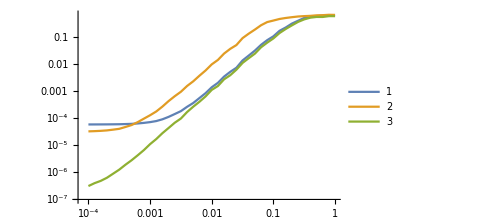

```mathematica
ListLogLogPlot[{Transpose[{ val,p}],Transpose[{ val,p2}],Transpose[{ val,p3}]},Joined->True,PlotRange->All,PlotLegends->Automatic,ImageSize->Medium]
```

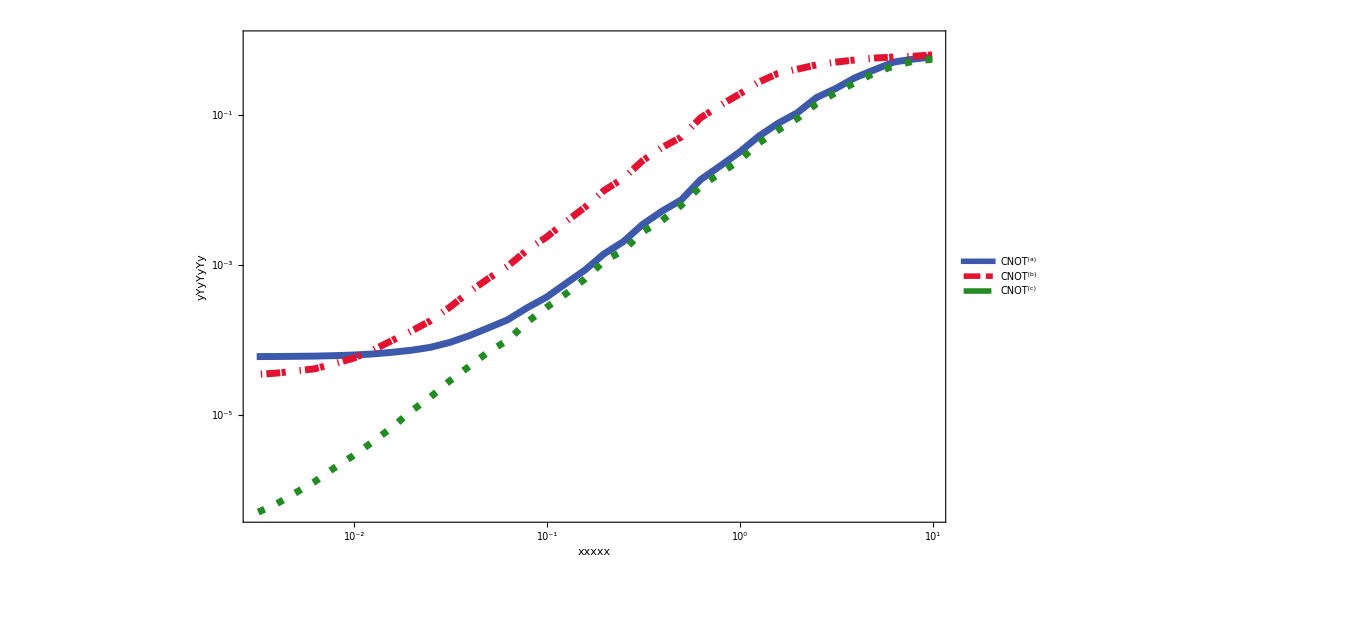

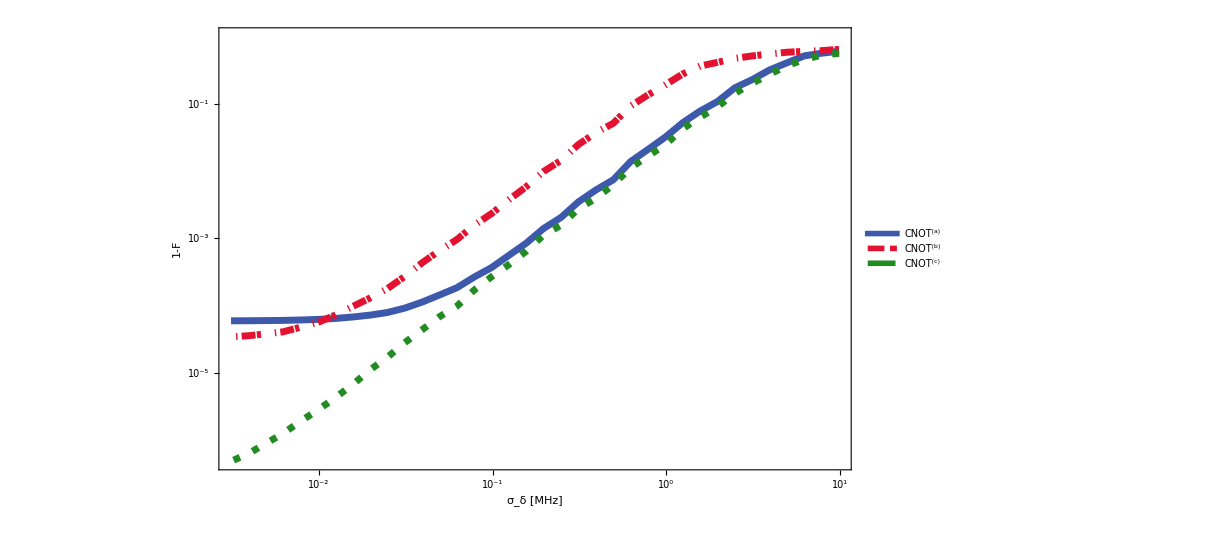

```mathematica
r = 4;
q = -3;
xTicks = LogTicks[10,-4,1,TickLengthScale->2,TickLabelStep->1];
xxTicks = LogTicks[10,-4,1,ShowTickLabels->False,TickLengthScale->2];
yTicks = LogTicks[10,-15,1,TickLabelStep->1,TickLengthScale->2,ShowMinorTicks->True];
yyTicks = LogTicks[10,-15,1,ShowTickLabels->False,TickLengthScale->2,ShowMinorTicks->True];
labelFontSize = 38;
legendFontSize = 32;
xLabel = "xxxxx";
yLabel = "yYyYyYy";
curveThickness = 5;

(* create legend *)
legend = Placed[{
Style["CNOT^(a)",legendFontSize],
Style["CNOT^(b)",legendFontSize],
Style["CNOT^(c)",legendFontSize]
},{{.7, .2}, {0, 0}}];


Show[
ListPlot[{Transpose[{Log10/@(J/((2π)10^6)(val[[r;;q]])),Log10/@(p[[r;;q]])}],Transpose[{Log10/@(J/((2π)10^6)(val[[r;;q]])),Log10/@(p2[[r;;q]])}],Transpose[{Log10/@(J/((2π)10^6)(val[[r;;q]])),Log10/@(p3[[r;;q]])}]},Joined->True,
PlotRange->All,LabelStyle->{FontFamily-> "Times"},
PlotStyle->{
{AbsoluteThickness[curveThickness],Cobalt},
{AbsoluteThickness[curveThickness],AbsoluteDashing[{3,1,10}],GeraniumLake},{AbsoluteThickness[curveThickness],AbsoluteDashing[{5,10}], ForestGreen},{AbsoluteThickness[curveThickness],AbsoluteDashing[{3,7,1}],Goldenrod}
},
PlotLegends->legend,Axes->False
],
LabelStyle->{FontFamily-> "Times"},ImageSize->{10^3,10^3},
FrameStyle->Directive[Thick,labelFontSize,Black],Frame->True,
FrameLabel->{Style[xLabel,labelFontSize],Style[yLabel,labelFontSize]},
FrameTicks->{xTicks,yTicks,xxTicks,yyTicks}
]
```

0.0447975

139.295

5.54498

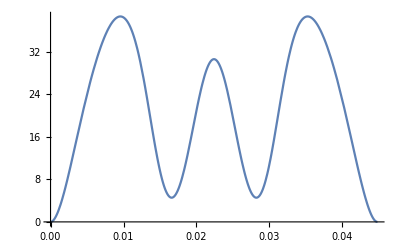

```mathematica
J= 2π 197/10;
A=139.29470064027242;
Δ=J;
τ=5.5449750444524115 1/Δ;
Bly1[t_]:=4/(2π)(((4 A t^2 (t-τ)^2 (14 t^2-14 t τ+3 τ^2))/τ^8)/(2 √(Δ^2/4-((4 A t^3 (t-τ)^3 (2 t-τ))/τ^8)^2))-√(Δ^2/4-((4 A t^3 (t-τ)^3 (2 t-τ))/τ^8)^2)Cot[2(A(t/τ)^4(1-t/τ)^4+π/4)]);

τ//N
A//N
τ Δ//N
Plot[Bly1[t],{t,0,τ}]
```

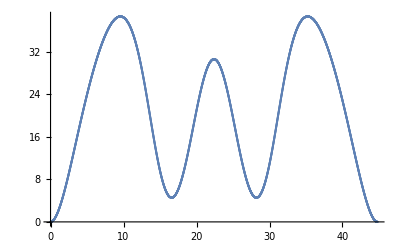

```mathematica
bly1=Table[Bly1[x],{x,0,τ,0.00001}];
tval=Table[1000i,{i,0,τ,0.00001}];
ListPlot[Transpose@{tval,bly1},PlotRange->All]
```

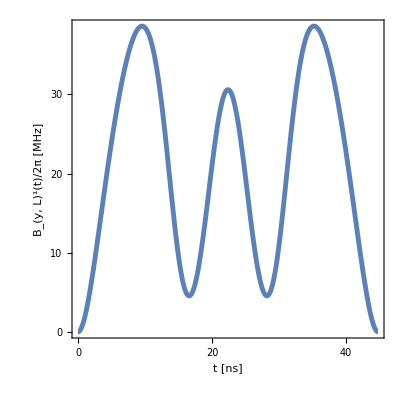

```mathematica
Block[{Ω,Ω1},
Show[ListPlot[Transpose@{tval,bly1},PlotRange->All,Joined->True,PlotStyle->{{AbsoluteThickness[3.5]},{AbsolutePointSize[0.5]},{AbsoluteThickness[3.5]}}],AspectRatio->1,FrameLabel->{Style["t [ns]",35,Black],Style["B_(y, L)^1(t)/2π [MHz]",35,Black]},LabelStyle->{FontFamily-> "Times"},ImageSize->{4 10^2,4 10^2},FrameStyle->Directive[AbsoluteThickness[1.4],35,Black],Frame->True,FrameTicks->{LinTicks[0,50,10,5,MajorTickLength-> 0.03,MinorTickLength-> 0.02],LinTicks[0,40,10,5,MajorTickLength-> 0.03,MinorTickLength-> 0.02, ShowFirst->True],StripTickLabels[LinTicks[0,50,10,3,MajorTickLength-> 0.02,MinorTickLength-> 0.015]],StripTickLabels[LinTicks[0,40,10,3,MajorTickLength-> 0.02,MinorTickLength-> 0.015]]}
]]
```